# how to use mathematica for cheg304

kyle wodehouse

everyone knows that mathematica is one of the most visually appealing and sexually arousing softwares in existence. it is of great interest to know how to whip out Mathematica to calculate (for example) t values in style. this is the purpose of this reference document.

## how do i find inverse cdf values? (critical t, chi)

mathematica makes life pretty easy for this because all of the distributions just exist within mathematica. and, naturally, how you get cdf values is literally the cdf[] function.

```mathematica
dist = StudentTDistribution[5,3]
```

StudentTDistribution[5,3]

don’t worry too much about how this is plotted, just admire its beauty

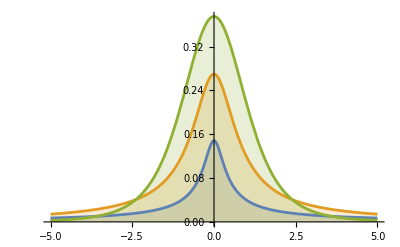

```mathematica
Plot[Table[PDF[StudentTDistribution[ν],x],{ν,{0.1,0.5,4}}]//Evaluate,{x,-5,5},Filling->Axis]
```

okay now let’s use this to find a critical t for 14 degrees of freedom at 95% for a two tail problem

```mathematica
Quantile[StudentTDistribution[14],0.975]
```

2.14479

what if i want a left tail 90% with 23 dof

```mathematica
Quantile[StudentTDistribution[23],0.1]
```

-1.31946

whaaaat about right tail 99 % at 7 dof

```mathematica
Quantile[StudentTDistribution[7],0.99]
```

2.99795

okay but what if i want to visualize the 90% quantile on the graph?

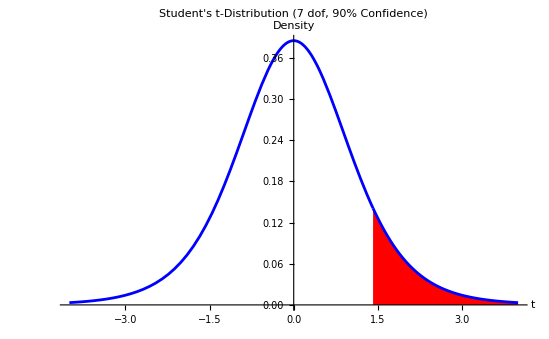

```mathematica
dist=StudentTDistribution[7];
tCrit=Quantile[dist,0.90];

Show[
Plot[PDF[dist,x],{x,-4,tCrit},Filling->None,PlotStyle->Blue,PlotRange->All,AxesLabel->{"t","Density"},PlotLabel->"Student's t-Distribution (7 dof, 90% Confidence)"],

Plot[PDF[dist,x],{x,tCrit,4},Filling->Axis,FillingStyle->Red,PlotStyle->Blue]
]
```

## how do i find integrals of prob dists?

this one is really fucking light. what if i want -infinity -> 1 of z dist?
 - make appropriate distribution
 - literally the integrate command

```mathematica
dist = PDF[NormalDistribution[],x]; (*  note that with no args normal -> z  *)
result = Integrate[dist,{x,-Infinity,1}]
N[result]
```

1/2 (1+Erf[1/(√2)])

0.841345